```mathematica
valRecLst=readJuliaVar["valRecLst1.jld2","valRecLst"];
```

```mathematica
valRecLst//Flatt
```

{1}

```mathematica
valRecLstNon0=readJuliaVar["valRecLstNon0.jld2","valRecLst"];
```

```mathematica
valRecLstNon0Div5=readJuliaVar["valRecLstNon0_div_5.jld2","valRecLst"];
```

```mathematica
valRecLstYes0Div5=readJuliaVar["valRecLstYes0_div_5.jld2","valRecLst"];
```

```mathematica
valRecLstYes0Div10=readJuliaVar["valRecLstYes0_div_10.jld2","valRecLst"];
```

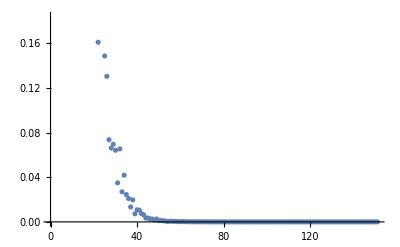

```mathematica
ListPlot[valRecLstYes0Div5ᵀ⟦1⟧]
```

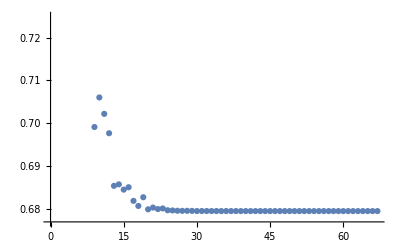

```mathematica
ListPlot[valRecLstNon0Div5ᵀ⟦1⟧]
```

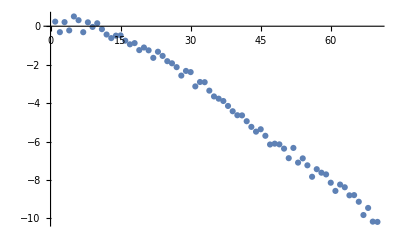

```mathematica
ListPlot[Log10[valRecLstNon0ᵀ⟦1⟧-valRecLstNon0ᵀ⟦1⟧⟦-1⟧]]
```

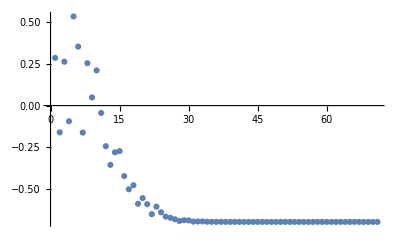

```mathematica
ListPlot[Log10[valRecLstNon0ᵀ⟦1⟧]]
```

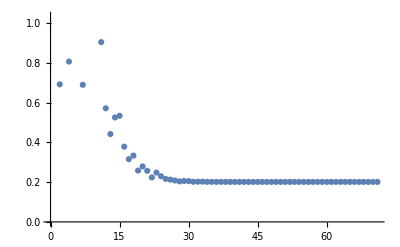

```mathematica
ListPlot[valRecLstNon0ᵀ⟦1⟧]
```

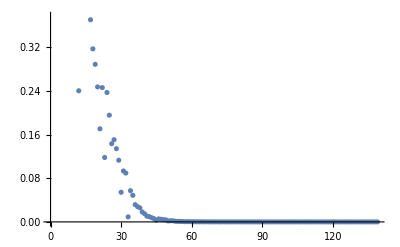

```mathematica
ListPlot[valRecLstᵀ⟦1⟧]
```

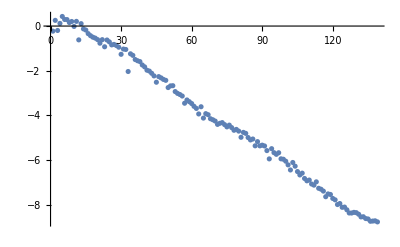

```mathematica
ListPlot[Log10[valRecLstᵀ⟦1⟧]]
```

```mathematica
Plot[valRecLst⟦1⟧]
```